```mathematica
Clear["Global`*"];
SetDirectory@NotebookDirectory[];
SetOptions[Notebooks["apportionment.nb"][[1]],AutoGeneratedPackage->Automatic]
```

# Apportionment Algorithms

Every ten years, after the decennial Census, the U.S. reallocates the 435 members of Congress based on updated state populations. This has major implications for both legislation and presidential elections, since a state's electoral votes are determined the size of its delegation. Is there a better way?

## Loading the Data

While Mathematica has population conveniently built in to state entities through the Wolfram Data Repository, let's be extra careful and use the same decennial Census figures the government has used for apportionment, as well as the official number of representatives per state allotted every tens years to compare to alternate methods. This data is conveniently organized on Census.gov and gathered in `getPopulationApportionment.nb`

```mathematica
(* statesByAbbreviation = Import["./data/state_population_reps_evs.wl"]; *)
statesByAbbreviation = CloudGet["https://www.wolframcloud.com/objects/1a4bfb31-d5d4-49e3-9e04-4cf80e1fae1b"];
stateAbbrs = Keys@statesByAbbreviation;
(* We need a list of state abbreviations without DC since it is not factored into allocation -- "Taxation Without Representation!" *)
stateAbbrs50 = Select[stateAbbrs, # != "DC"&];
```

## How it works now: The Huntington-Hill method

Since the 1940 Census, the United States has used the Huntington-Hill algorithm, known as the "method of equal proportions," to divvy up the 435 House seats. This begins by allotting one electoral vote to each state, leaving 385 left. The 50 states are then allotted these remaining seats one-by-one according to which one has the highest priority as determined by a simple equation: its population divided by the square root of its current seats times one extra seat (the Geometric Mean):

P/(√(n (1+n)))

"https://en.wikipedia.org/wiki/United_States_congressional_apportionment#The_method_of_equal_proportions""https://en.wikipedia.org/wiki/United_States_congressional_apportionment#The_method_of_equal_proportions"

Let's make this equation a function for a given state, getting the 2010 decennial Census data from the data we loaded and feeding it the current number of allocated seats

```mathematica
priorityHuntingtonHill[stateAbbr_, stateReps_] := 
	1.0 * statesByAbbreviation[stateAbbr]["population_decennial"]["2010"] / Sqrt[stateReps * (stateReps + 1)]
```

The allocation function will assign electoral votes according to the above formula one at a time. We're also going to explicitly pass the priority function in case we want to try a different one later, which we definitely will, and parameterize all aspects of the allocation algorithm:

To save time, we' re also going to store the priorities until we update the number of seats in a state rather than run 50 square roots 385 times.

total_ is the total number of seats to allocate, defaulting to 435

min_ is the default number of seats that every state begins with, defaulting to 1

bonus_ is the number of seats every state gets at the end of the process, after total_ is depleted. Default is 0. Setting to 2 calculates electoral votes by accounting for senators, so long as you remember to add 3 for Washington, D.C.!

priorityFunc_ is the means of determining a state's priority, defaulting to the Huntington-Hill function defined above

```mathematica
AllocateOne[reps_, priorities_, priorityFunc_:priorityHuntingtonHill] := (
	topPriority = First[Keys[Reverse[Sort[priorities]]]];
	updatedPriorities = priorities;
	updatedReps = reps;
	updatedReps[topPriority] += 1;
	updatedPriorities[topPriority] = priorityFunc[topPriority, updatedReps[topPriority]];
	{ updatedReps, updatedPriorities }
);

calculateAllocations[totalBase_:435, min_:1, bonus_:0, priorityFunc_:priorityHuntingtonHill]:= (
	total = totalBase + 50 * -bonus; (* we need to add the post-facto bonus to the total so that it doesn't count against it *)
	stateReps = AssociationThread[stateAbbrs50, ConstantArray[min, 50]];
	statePriorities = AssociationThread[stateAbbrs50, priorityFunc[#, 1]& /@ stateAbbrs50];
	While[Total@stateReps < total, { stateReps, statePriorities } = AllocateOne[stateReps, statePriorities, priorityFunc]];
	stateReps = stateReps + bonus;
	KeySort@stateReps
);
```

## Getting and mapping the effects of our calculations

We need to be able to compare our results to the real apportionment, both to check our algorithm and see how modifications change it.

Here’s a few colors we’ll be using

```mathematica
{ lightOrange, darkOrange, green, purple, lightGray } = { RGBColor["#FFA63B"], RGBColor["#FF703B"], RGBColor["#47C045"], RGBColor["#E165FA"], RGBColor["#DCDCDC"] }
```

{RGBColor[1., 0.6509803921568628, 0.23137254901960785],RGBColor[1., 0.4392156862745098, 0.23137254901960785],RGBColor[0.2784313725490196, 0.7529411764705882, 0.27058823529411763],RGBColor[0.8823529411764706, 0.396078431372549, 0.9803921568627451],RGBColor[0.8627450980392157, 0.8627450980392157, 0.8627450980392157]}

```mathematica
houseOfRepresentatives = AssociationThread[
	stateAbbrs50,
	statesByAbbreviation[#]["representatives"]["2010"]& /@ stateAbbrs50
];
```

```mathematica
getDiffs[calculatedReps_] := calculatedReps - houseOfRepresentatives;
```

We're going to optionally include the ability to sort the results

```mathematica
makeRows[calculatedReps_, sortBy_:"alpha", ascendDescend_:-1] := (
	diffs = getDiffs[calculatedReps];
	stateKeys = Keys@houseOfRepresentatives;
	
	(* now we can sort. This is like a `Switch` statement, but a little easier to read *)
	sortRules = <|
		"alpha" -> If[ascendDescend == -1, Sort@Keys@houseOfRepresentatives, Reverse@Sort@Keys@houseOfRepresentatives],
		"actual" -> If[ascendDescend == -1, Keys[Sort@houseOfRepresentatives], Keys[Reverse@Sort@houseOfRepresentatives]],
		"yours" -> If[ascendDescend == -1, Keys[Sort@calculatedReps], Keys[Reverse@Sort@calculatedReps]],
		"delta" -> If[ascendDescend == -1, Keys[Sort@diffs], Keys[Reverse@Sort@diffs]]
	|>;

	stateNames = sortRules[sortBy];
		
	maxDiff = Max[diffs];
	maxDiff = If[maxDiff == 0, 2, maxDiff];
		
	colorScales = {
		Function[d, White], (* states, always white *)
		Function[d, Blend[Transpose[{{-10, Max[houseOfRepresentatives]}, { White, lightOrange }}], d]], (* actual house, max is 53 *)
		Function[d, Blend[Transpose[{{-10, Max[calculatedReps]}, { White, darkOrange }}], d]], (* user calculations *)
		Function[d, Blend[Transpose[{{-maxDiff, 0, maxDiff}, { green, White, purple }}], d]] (* diffs, green for losing seats, purple for gaining *)	
	};
	
	(* convert the seating data to items for grid, adding header and footer *)	
	dataAssociations = { AssociationThread[stateNames, stateNames], houseOfRepresentatives, calculatedReps, diffs };

	heightCell = 1;
	widthCell = 2;
	
	(* convert each cell to an Item for easier formatting *)
	itemizeCell[{ dataAssociation_, colorScale_ }] := Item[Style[dataAssociation[#], FontSize->12, TextAlignment->Center],
		Background->colorScale[dataAssociation[#]],
		ItemSize->{ widthCell, heightCell },
		Alignment -> Bottom]&
	/@ stateNames;
	
	itemizedRows = Map[
		itemizeCell,
		Transpose[{ dataAssociations, colorScales }]
	];
	
	totals = { "Total", Total@houseOfRepresentatives, Total@calculatedReps, Total@diffs };
	Append[itemizedRows[[#]], Item[totals[[#]], ItemSize->{2 * widthCell, heightCell}]]& /@ Range[4]
)
```

```mathematica
horizontalGrid[rows_, perRow_:13] := (
	(* build rows of grids *)
	headers = Item[#, Alignment -> Right, ItemSize->{4, 1}]& /@ { "state", "Actual", "Yours", "delta" };
	parts = First@Partition[rows, { 4, UpTo@perRow }];
	headerRows = Map[Flatten, Transpose[{ headers, # }]& /@ parts, {2}];
	Column[Grid[#, Frame -> All, ItemSize->All, Spacings->{0.2, 0.8}]& /@ headerRows, Spacings -> -0.1]
)
```

### Okay, time to test it!

For a test case, let’s start with making sure we get the same results as we expect under current law.

```mathematica
gutCheck = calculateAllocations[435, 1, 0];
horizontalGrid[makeRows[gutCheck]]
```

Then we’ll try factoring in the full electoral votes in the allotment and then subtract them at the end.

```mathematica
factorInElectors = calculateAllocations[435, 3, -2];
horizontalGrid[makeRows[factorInElectors]]
```

## Let’s map it too

```mathematica
mapDiffs[calculatedReps_] := (
	entityDiffs = KeyMap[statesByAbbreviation[#]["entity"]&, getDiffs[calculatedReps]];
	green = RGBColor["#47C045"];
	purple = RGBColor["#E165FA"];
	max = Max[entityDiffs];
	max = If[max == 0, 2, max];
	
	colorScheme = Function[d, Blend[Transpose[{{-max, 0, max}, { green, White, purple }}], d]];
	
	contentinal = GeoRegionValuePlot[entityDiffs, GeoRange->Entity["Country","UnitedStates"], ImageSize->499, PlotLegends->None, ColorFunction->colorScheme, ColorFunctionScaling -> False];
	ak = GeoRegionValuePlot[entityDiffs, GeoRange->Entity["AdministrativeDivision",{"Alaska","UnitedStates"}], ImageSize->249, PlotLegends->None, ColorFunction->colorScheme, ColorFunctionScaling -> False];
	hi = GeoRegionValuePlot[entityDiffs, GeoRange->Entity["AdministrativeDivision",{"Hawaii","UnitedStates"}], GeoRangePadding -> {Quantity[30, "Kilometers"], Quantity[50, "Kilometers"]}, ImagePadding->{{5,0},{0,0}}, GeoRangePadding -> {Scaled[0], None}, ImageSize->250, PlotLegends->None, ColorFunction->colorScheme, ColorFunctionScaling -> False];
	Column[{
		Row[{
			Column[{
				Row[{ contentinal }, ImageSize->500],
				Row[{ak,hi}, ImageSize->500]
			}],
			BarLegend[{colorScheme, {-max, max}}, LegendMarkerSize->300]
		}],
		horizontalGrid[makeRows[calculatedReps], 17]
	}]
)
```

Allowing for the electors benefits the larger-population states

```mathematica
mapDiffs[factorInElectors]
```

```mathematica
Manipulate[
	mapDiffs[calculateAllocations[total, min, bonus, priorityHuntingtonHill]],
	{{ total, 435, "Total Reps:"}, 50, 2000, 1, Appearance -> "Open" },
	{{ min, 3, "Start With:"}, 0, 40, 1, Appearance -> "Open" },
	{{ bonus, -2, "Add at End:"}, -5, 20, 1, Appearance -> "Open" },
	LabelStyle->{ FontSize -> 13 }
]
```

## Analyzing the number of people per representative

Another way to measure the effectiveness of allocation is by measuring the ratio of the population to its number of representatives. We have the population conveniently baked in to the state data, so we’ll add a bar chart to the visualization.

```mathematica
statePopulations = AssociationThread[
	stateAbbrs50,
	statesByAbbreviation[#]["population_decennial"]["2010"]& /@ stateAbbrs50
];
totalUSPopulation = Total@statePopulations; (* won't count DC or PR since we have no reps *)
```

Function for calculating the population per representative.

```mathematica
peoplePerRepresentative[allocation_] := (
	perRep = AssociationThread[
		stateAbbrs50,
		Round[statePopulations[#] / allocation[#] * 1.0]& /@ stateAbbrs50
	]
)
```

```mathematica
visualizeRepresentation[calculatedReps_, sortBy_:"perRepCalculated", ascendDescend_:-1] := (
	stateKeys = Keys@houseOfRepresentatives;
	
	(* data *)
	perRepHouse = peoplePerRepresentative[AssociationThread[stateKeys, houseOfRepresentatives[#]& /@ stateKeys]];
	perRepCalculated = peoplePerRepresentative[AssociationThread[stateKeys, calculatedReps[#]& /@ stateKeys]];
	
	(* now we can sort. This is like a `Switch` statement, but a little easier to read *)
	sortRules = <|
		"perRepHouse" -> If[ascendDescend == 1, Keys[Sort@perRepHouse], Keys[Reverse@Sort@perRepHouse]],
		"perRepCalculated" -> If[ascendDescend == 1, Keys[Sort@perRepCalculated], Keys[Reverse@Sort@perRepCalculated]]
	|>;			

	stateNames = sortRules[sortBy];
		
	(* BAR CHARTS *)	
	chartWidth = 900;
	chartHeight = 300;
	chartAspect = chartHeight / chartWidth;
		
	makeBarChart = Function[{ assoc, seats, xMax }, (
		labeledData  = Labeled[assoc[#], Rotate[Style[ToString@seats[#] <> " REPS", LightGray], Pi / 2], Top]& /@ Reverse@stateNames;
		BarChart[
			labeledData,
			ColorFunction -> "Rainbow",
			ChartLabels -> stateNames,
			ImageSize -> chartWidth,
			AspectRatio -> chartAspect,
			GridLines -> { None, Automatic },
			Frame -> True,
			FrameTicks -> { 0, 0 },
			FrameLabel -> None,
			BarSpacing -> 0.2,
			PlotRange -> { 0, Automatic },
			PlotRangePadding -> { {0, 0 }, { 0, 1.25 }}
		]
	)];
	
	barChartHouse = makeBarChart[perRepHouse, houseOfRepresentatives, 800000];
	barChartCalculated = makeBarChart[perRepCalculated, calculatedReps, Max[perRepCalculated]];

	(* headers for charts *)	
	covHouse = StandardDeviation[perRepHouse] / Mean@perRepHouse * 1.0;
	labelHouse = Column[{
		Style["People Per Representative", FontSize -> 12],
		Style["Actual Congress", FontSize -> 16, Darker@Red, Bold],
		Grid[{{ Style["Coeff. of Var.: ", FontSize -> 12], Framed[Style[ToString@covHouse, FontSize->14, Bold], Background->Yellow]}}]
	}, Alignment -> Center];

	covCalculated = StandardDeviation[perRepCalculated] / Mean@perRepCalculated * 1.0;
	labelCalculated = Column[{
		Style["People Per Representative", FontSize -> 12],
		Style["Your Recalculation", FontSize -> 16, Darker@Red, Bold],
		Grid[{{ Style["Coeff. of Var.: ", FontSize -> 12], Framed[Style[ToString@covCalculated, FontSize->14, Bold], Background->Yellow]}}]
	}, Alignment -> Center];
	
	columns = {
		labelHouse, barChartHouse, labelCalculated, barChartCalculated
	};

	display = Column[columns, Alignment->Center]
)
```

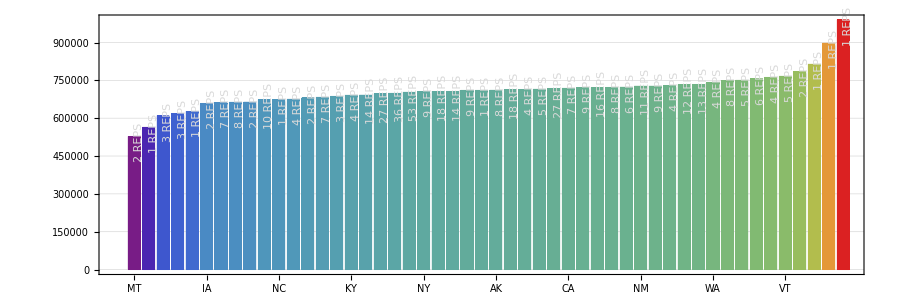
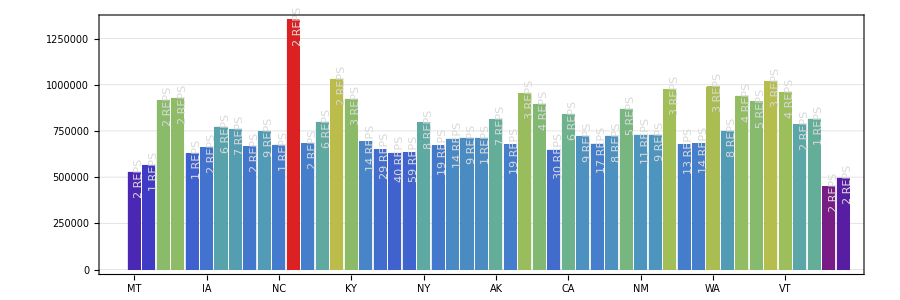
People Per Representative
Actual Congress
Coeff. of Var.:  | 0.0990053
-Graphics-
People Per Representative
Your Recalculation
Coeff. of Var.:  | 0.207875
-Graphics-

```mathematica
visualizeRepresentation[factorInElectors, "perRepHouse", -1]
```

```mathematica
visualizeCalculation[calculated_] := (		
	sortOn = "alpha";
	ascendDescend = -1;
	rows = {};
		
	sortables = {
		"alpha" -> "Alphabetical",
		"actual" -> "Current Allocation",
		"yours" -> "Calculated Allocations",
		"delta" -> "Difference",
		"perRepHouse" -> "Per Rep: Actual",
		"perRepCalculated" -> "Per Rep: Calculated"	
	};
		
	(*		
	DynamicModule[{sortOn, ascendDescend}, ( 
	
		sortMenu = PopupMenu[Dynamic[sortOn], sortables];
		ascendDescendSelector = RadioButtonBar[Dynamic[ascendDescend], { -1 -> "Ascending", 1 -> "Descending" }];
		
		;

		
		
		;
		
		rows = visualizeAllocation[calculated, s, d];
		grid = Grid[
			Prepend[
				rows, 
				{Row[{ sortMenu, ascendDescendSelector }], SpanFromLeft, SpanFromLeft }
			], Frame->All, Alignment->Top
		]
		
	), DynamicModuleValues -> True];*)
	
	sortMenu = PopupMenu[Dynamic[sortOn], sortables];
	
	ascendDescendSelector = RadioButtonBar[Dynamic[ascendDescend], { -1 -> "Ascending", 1 -> "Descending" }];
	
	(*
	rows = visualizeAllocation[calculated, Dynamic@sortOn, Dynamic@ascendDescend];
	*);
	rows = Dynamic[sortOn, visAll[calculateAllocations, sortOn, ascendDescend], visualizeAllocation[calculateAllocations, sortOn, ascendDescend]];
	
	Grid[{ sortMenu, ascendDescendSelector }]
)
```

```mathematica
visualizeCalculation[bigHouse]
```

{String,Integer}

Sort::normal: Nonatomic expression expected at position 1 in Sort[calculateAllocations].

Keys::invrl: The argument Sort[calculateAllocations] is not a valid Association or a list of rules.

stateNames

{AK,AL,AR,AZ,CA,CO,CT,DE,FL,GA,HI,IA,ID,IL,IN,KS,KY,LA,MA,MD,ME,MI,MN,MO,MS,MT,NC,ND,NE,NH,NJ,NM,NV,NY,OH,OK,OR,PA,RI,SC,SD,TN,TX,UT,VA,VT,WA,WI,WV,WY}

Total::normal: Nonatomic expression expected at position 1 in Total[calculateAllocations].

Blend::arg: {{-10,GrayLevel[1]},{calculateAllocations,RGBColor[1., 0.4392156862745098, 0.23137254901960785]}} is not a valid list of colors or images, or pairs of a real number and a color or an image.

General::stop: Further output of Blend::arg will be suppressed during this calculation.

Grid[{, | Ascending   | Descending}]

## Wrapping up

We now have all the tools we need to play with different ways to configure the House. We'll import this Notebook into a playpen and get started.